```mathematica
AppendTo[$Path, NotebookDirectory[]];
```

```mathematica
Get["CubeAcquire.wl"]
Get["CubeVisualize.wl"]
Get["CubeCore.wl"]
```

```mathematica
cubeString = sampleStrings["solved"]
```

WWWWWWWWWOOOGGGRRRBBBOOOGGGRRRBBBOOOGGGRRRBBBYYYYYYYYY

## 2D Cube

```mathematica
cube2D = Generate2DCube[cubeString];
```

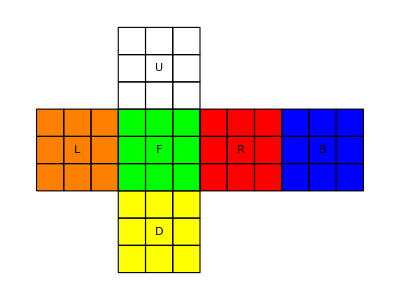

```mathematica
Visualize2DCube[cube2D];
```

## 3D Cube

```mathematica
cube3DPieces = GetPieces[cubeString];
```

```mathematica
cube3D = Dynamic[Generate3DCube[cube3DPieces]];
```

```mathematica
Visualize3DCube[cube3D];
```

-Graphics3D-

### Controlli

#### Generale

```mathematica
List[
Button["Load solved",cube3DPieces=GetPieces[sampleStrings["solved"]];],
Button["Load start",cube3DPieces=GetPieces[sampleStrings["start"]];]
]
```

{Load solved,Load start}

#### Mosse standard cubo

```mathematica
List[Button["L",cube3DPieces=RotateL[cube3DPieces];],Button["L'",cube3DPieces=RotateLi[cube3DPieces];],Button["R",cube3DPieces=RotateR[cube3DPieces];],Button["R'",cube3DPieces=RotateRi[cube3DPieces];],Button["U",cube3DPieces=RotateU[cube3DPieces];],Button["U'",cube3DPieces=RotateUi[cube3DPieces];],Button["D",cube3DPieces=RotateD[cube3DPieces];],Button["D'",cube3DPieces=RotateDi[cube3DPieces];],Button["F",cube3DPieces=RotateF[cube3DPieces];],Button["F'",cube3DPieces=RotateFi[cube3DPieces];],Button["B",cube3DPieces=RotateB[cube3DPieces];],Button["B'",cube3DPieces=RotateBi[cube3DPieces];]]
```

{L,L',R,R',U,U',D,D',F,F',B,B'}

#### Rotazione cubo

```mathematica
List[Button["X",cube3DPieces=RotateX[cube3DPieces];],Button["X'",cube3DPieces=RotateXi[cube3DPieces];],Button["Y",cube3DPieces=RotateY[cube3DPieces];],Button["Y'",cube3DPieces=RotateYi[cube3DPieces];],Button["Z",cube3DPieces=RotateZ[cube3DPieces];],Button["Z'",cube3DPieces=RotateZi[cube3DPieces];]]
```

{X,X',Y,Y',Z,Z'}

```mathematica
(* get cubes idxs *)
getCube[total_, element_] := (First[Position[total, element]]);
getPos[total_, elements_, pattern_]:=(
idxs=Flatten[
Position[
Table[
Flatten[
Cases[{elements[[t]]["pos"]},pattern]],{t,1,Length[elements]}],
pattern]];
 Return[
Flatten[
Table[
getCube[total, elements[[idxs[[t]]]]], {t,1,Length[idxs]}]
]]);
getCol[total_,elements_, pattern_] := (
idxs=Flatten[
Position[
Table[
Flatten[
Cases[{elements[[t]]["colors"]},pattern]],{t,1,Length[elements]}],
pattern]];
Return[
Flatten[
Table[
getCube[total, elements[[idxs[[t]]]]], {t,1,Length[idxs]}]
]]);

numberOfNone=Table[Count[cube3DPieces[[t]]["colors"],None],{t,1,Length[cube3DPieces]}];
idxOfEdges=Flatten[Position[numberOfNone,1]];
idxWhiteEdges=getCol[cube3DPieces,cube3DPieces[[idxOfEdges]],{___,"W",___}]
idxSecondFloorWhiteEdges=getPos[cube3DPieces,cube3DPieces[[idxWhiteEdges]],{_,0,_}];
SFwhiteEdges=cube3DPieces[[idxSecondFloorWhiteEdges]];
(* Find yellow center cube *)
patternYcenter={None,"Y",None};
yCenter=First[Position[Table[cube3DPieces[[t]]["colors"],{t,1,Length[cube3DPieces]}],patternYcenter]];
yCubeCenter = cube3DPieces[[yCenter]];
idxSecondFloorWhiteEdges=getPos[cube3DPieces,cube3DPieces[[idxWhiteEdges]],{_,0,_}];
SFwhiteEdges=cube3DPieces[[idxSecondFloorWhiteEdges]];
daisyFirst[element_]:= (
checkX = element["colors"][[1]] == "W";
(*cubes = {getPos[cube3DPieces, cube3DPieces, {1,1,-1}],
getPos[cube3DPieces, cube3DPieces, {1,1,1}],
getPos[cube3DPieces, cube3DPieces, {-1,1,1}],
getPos[cube3DPieces, cube3DPieces, {-1,1,-1}]};*)
Switch[element["pos"],
{1,0,1},
(If[checkX , (cube3DPieces=RotateFi[cube3DPieces];Return["F'"]), (cube3DPieces=RotateR[cube3DPieces];Return["R"])]), 
{-1,0,1},
If[checkX, (cube3DPieces=RotateF[cube3DPieces];Return["F"]), (cube3DPieces=RotateLi[cube3DPieces];Return["L'"])],
{1,0,-1},
If[checkX, (cube3DPieces=RotateB[cube3DPieces];Return["B"]), (cube3DPieces=RotateRi[cube3DPieces];Return["R'"])],
{-1,0,-1},
If[checkX, (cube3DPieces=RotateBi[cube3DPieces];Return["B'"]), (cube3DPieces=RotateL[cube3DPieces];Return["L"])]]
);
Table[daisyFirst[SFwhiteEdges[[t]]],{t,1,Length[SFwhiteEdges]}]
```

{7,8,9,18}

{F'}

```mathematica
{7,8,9,18}
```

{7,8,9,18}

{<|pos→{1,0,1},colors→{W,None,G}|>}

Set::setraw: Cannot assign to raw object <|pos→{1,0,0},colors→{R,None,None}|>.

Set::setraw: Cannot assign to raw object <|pos→{-1,0,0},colors→{O,None,None}|>.

Set::setraw: Cannot assign to raw object <|pos→{0,1,0},colors→{None,Y,None}|>.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

{F'}

```mathematica
freePark[element_]:=(
	
)
```